4

Read::readn: Invalid real number found when reading from notes2.txt.

Set::shape: Lists {letter,octave,accidental,len1,len2} and $Failed are not the same shape.

Read::readn: Invalid real number found when reading from notes2.txt.

Set::shape: Lists {letter,octave,accidental,len1,len2} and $Failed are not the same shape.

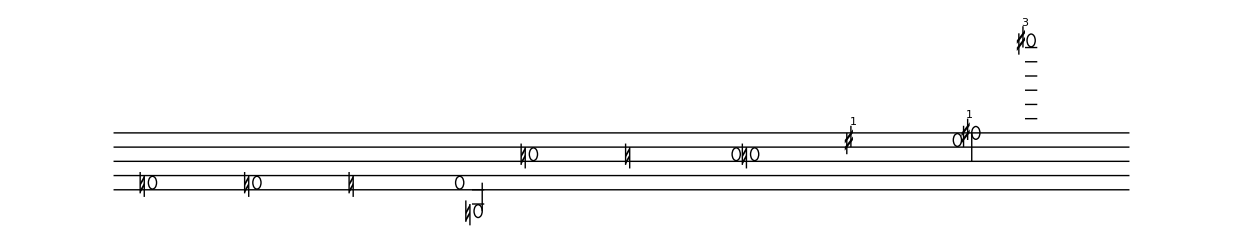

```mathematica
drawStaff[cent_,len_]:={Line[{{0,cent+4},{len,cent+4}}],Line[{{0,cent+2},{len,cent+2}}],Line[{{0,cent},{len,cent}}],Line[{{0,cent-2},{len,cent-2}}],Line[{{0,cent-4},{len,cent-4}}]};

drawBar :=
(horzPos =nextPos;
nextPos += spacing ;
beatCount = 0;
{Thickness[.01],Line[{{horzPos,center+4},{horzPos,center-4}}]})

drawWholeNote[step_] :=
(horzPos =nextPos;
nextPos += 8*spacing ;
If[beatCount > meter, drawBar];
beatCount +=4;

{Circle[{horzPos, step}, {1,.9}]})
drawHalfNoteDown[step_] :=
(horzPos =nextPos;
nextPos += 4*spacing ;
{Circle[{horzPos, step},{1,.9}], Line[{{horzPos-1,step},{horzPos-1,step-4}}]})
drawHalfNoteUp[step_] :=
(horzPos =nextPos;
nextPos += 4*spacing ;
{Circle[{horzPos, step},{1,.9}], Line[{{horzPos+1,step},{horzPos+1,step+4}}]})
drawQuarterNoteDown[step_] :=
(horzPos =nextPos;
nextPos += 2*spacing ;
{Disk[{horzPos, step},{1,.9}], Line[{{horzPos-1,step},{horzPos-1,step-4}}]})
drawQuarterNoteUp[step_] :=
(horzPos =nextPos;
nextPos += 2*spacing ;
{Disk[{horzPos, step},{1,.9}], Line[{{horzPos+1,step},{horzPos+1,step+4}}]})
drawEigthNoteUp[step_] :=
(horzPos =nextPos;
nextPos += 1*spacing ;
{Disk[{horzPos, step},{1,.9}], Line[{{horzPos+1,step},{horzPos+1,step+4}}], FilledCurve[BezierCurve[{{horzPos+1,step+4},{horzPos+1,step+3},{horzPos+3,step+2},{horzPos+2,step+1},{horzPos+3,step+1.5}, {horzPos+1,step+3},{horzPos+1,step+2.5}}]]})
drawEigthNoteDown[step_] :=
(horzPos =nextPos;
nextPos += 1*spacing ;
{Disk[{horzPos, step},{1,.9}], Line[{{horzPos-1,step},{horzPos-1,step-4}}],
FilledCurve[BezierCurve[{{horzPos-1,step-4},{horzPos-1,step-3},{horzPos+1,step-2},{horzPos,step-1},{horzPos+1,step-1.5}, {horzPos-1,step-3},{horzPos-1,step-2.5}}]]})
drawSixteenthNoteUp[step_] :=
(horzPos =nextPos;
nextPos += 1*spacing ;
{Disk[{horzPos, step},{1,.9}], Line[{{horzPos+1,step},{horzPos+1,step+4}}], FilledCurve[BezierCurve[{{horzPos+1,step+4},{horzPos+1,step+3},{horzPos+3,step+2},{horzPos+2,step+1},{horzPos+3,step+1.5}, {horzPos+1,step+3},{horzPos+1,step+2.5}}]],FilledCurve[BezierCurve[{{horzPos+1,step+5},{horzPos+1,step+4},{horzPos+3,step+3},{horzPos+2,step+2},{horzPos+3,step+2.5}, {horzPos+1,step+4},{horzPos+1,step+3.5}}]]})
drawSixteenthNoteDown[step_] :=
(horzPos =nextPos;
nextPos += 1*spacing ;
{Disk[{horzPos, step},{1,.9}], Line[{{horzPos-1,step},{horzPos-1,step-4}}],
FilledCurve[BezierCurve[{{horzPos-1,step-4},{horzPos-1,step-3},{horzPos+1,step-2},{horzPos,step-1},{horzPos+1,step-1.5}, {horzPos-1,step-3},{horzPos-1,step-2.5}}]],FilledCurve[BezierCurve[{{horzPos-1,step-5},{horzPos-1,step-4},{horzPos+1,step-3},{horzPos,step-2},{horzPos+1,step-2.5}, {horzPos-1,step-4},{horzPos-1,step-3.5}}]]})

drawSharp[step_, num_]:=
(If[num == 0, drawNatural[step],
horzPos =nextPos;
nextPos += .5*spacing ;
{Text[num,{horzPos,step+2.5}],Polygon[{{horzPos -2,step-1},{horzPos -2,step-1.5},{horzPos ,step},{horzPos ,step+.5}}],Polygon[{{horzPos -2,step},{horzPos -2,step -.5},{horzPos ,step +1},{horzPos ,step+1.5}}],
Line[{{horzPos -1.5,step+1},{horzPos -1.5,step-2}}],Line[{{horzPos -.5,step-1},{horzPos -.5,step+2}}]}])
drawFlat[step_, num_]:=
(If[num == 0, drawNatural[step],
horzPos =nextPos;
nextPos += .5*spacing ;
{Text[num,{horzPos,step+2.5}],Line[{{horzPos -1,step-1},{horzPos -1,step+3}}],FilledCurve[BezierCurve[{{horzPos-1,step -1},{horzPos +1,step},{horzPos+1,step+2},{horzPos-1,step+1},{horzPos,step+1},{horzPos,step},{horzPos-1,step -1}}]]}])
drawNatural[step_]:=
(horzPos =nextPos;
nextPos += .5*spacing ;
{Polygon[{{horzPos - 1.5,step-1},{horzPos -1.5,step-1.5},{horzPos -.5,step-.5},{horzPos -.5,step}}],Polygon[{{horzPos -1.5,step},{horzPos -1.5,step -.5},{horzPos -.5,step +.5},{horzPos -.5 ,step+1}}],
Line[{{horzPos -1.5,step+1.5},{horzPos -1.5,step-1.5}}],Line[{{horzPos -.5,step-2},{horzPos -.5,step+1}}]})


drawHalfNote[step_] :=
(If[step > center,drawHalfNoteDown[step],drawHalfNoteUp[step]]
)
drawQuarterNote[step_] :=
(If[step > center,drawQuarterNoteDown[step],drawQuarterNoteUp[step]]
)
drawEigthNote[step_] :=
(If[step > center,drawEigthNoteDown[step],drawEigthNoteUp[step]]
)
drawSixteenthNote[step_] :=
(If[step > center,drawSixteenthNoteDown[step],drawSixteenthNoteUp[step]]
)


drawWholeRest[step_] :=
(horzPos =nextPos;
nextPos += 8*spacing ;
{Polygon[{{horzPos - 1.25,step},{horzPos -.75,step-1},{horzPos +.75,step-1},{horzPos +1.25,step}}]})
drawHalfRest[step_] :=
(horzPos =nextPos;
nextPos += 4*spacing ;
{Polygon[{{horzPos - 1.25,step -2},{horzPos -.75,step-1},{horzPos +.75,step-1},{horzPos +1.25,step-2}}]})
drawQuarterRest[step_] :=
(horzPos =nextPos;
nextPos += 2*spacing;
{FilledCurve[BezierCurve[{{horzPos+1,step +1},{horzPos -1,step+2},{horzPos+2,step+3},{horzPos,step+4},{horzPos+1,step+3},{horzPos -2,step+2},{horzPos+1,step +1}}]],
FilledCurve[BezierCurve[{{horzPos+1,step -1},{horzPos -1,step},{horzPos-1,step+2},{horzPos+1,step+1},{horzPos,step+1},{horzPos,step},{horzPos+1,step -1}}]]})
drawEigthRest[step_] :=
(horzPos =nextPos;
nextPos += 2*spacing;
{Disk[{horzPos -1, step},.5], BezierCurve[{{horzPos-1.5,step },{horzPos -.5 ,step -1},{horzPos +.5,step}}], Line[{{horzPos +.5,step},{horzPos -1 ,step -3}}]})
drawSixteenthRest[step_] :=
(horzPos =nextPos;
nextPos += 2*spacing;
{Disk[{horzPos -1, step},.5], BezierCurve[{{horzPos-1.5,step },{horzPos -.5 ,step -1},{horzPos +.5,step}}], Disk[{horzPos -.5, step +1},.5], BezierCurve[{{horzPos-1,step +1},{horzPos  ,step },{horzPos +1,step+1}}],Line[{{horzPos +1,step +1},{horzPos -1 ,step -3}}]})




convertNote2Num[l_] := l/.{A-> -3, B->-2, C-> -1, D -> 0, E -> 1, F-> 2, G->3,"A"-> -3, "B"->-2, "C"-> -1, "D" -> 0, "E" -> 1, "F"-> 2, "G"->3}

drawLedgerLineUp[step_] := {Table[Line[{{horzPos -1.5,i},{horzPos+1.5,i}}], {i,topLine, step,2}]}
drawLedgerLineDn[step_] := {Table[Line[{{horzPos -1.5,i},{horzPos+1.5,i}}], {i,lowLine, step,-2}]}

drawNote[note_, oct_, accitype_,acci_,len_] :=
(step = convertNote2Num[note] + oct*7;
{Switch[accitype,
sharp,drawSharp[step,acci],
flat,drawFlat[step,acci],
natural, drawNatural[step],
_,
]
,
Switch[len, 
1, drawWholeNote[step], 
1/2,drawHalfNote[step],
1/4,drawQuarterNote[step],
1/8,drawEigthNote[step],
1/16,drawSixteenthNote[step],
_,
]
,If[step > topLine, drawLedgerLineUp[step]]
,If[step < lowLine, drawLedgerLineDn[step]]
}

)

drawRest[len_]:=
(step = center;
Switch[len, 
1, drawWholeRest[step], 
1/2,drawHalfRest[step],
1/4,drawQuarterRest[step],
1/8,drawEigthRest[step],
1/16,drawSixteenthRest[step],
_,]
)



drawTrebClef :=
{Disk[{1.5,-1},.75], BezierCurve[{{.75,-1},{1,-3},{4,-3},{4,-1},{3.75,0}}], Line[{{3.75,0},{2,8}}],
BezierCurve[{{2,8},{2,9},{3,10},
{3,10},{4,9},{3,7},
{2,5},{1,4},{0,2},
{1,1},{3,0},{6,1},{4,4}, 
{2,4}, {2,2}, {2,3}
}]
}
(*drawBassClef
drawAltoClef
drawTenorClef
*)


(***************************SETUP THE VARIABLES***************************)
spacing = 3;
topLine = 11;
lowLine = 1;
frontbuffer = 5;
horzPos = spacing+frontbuffer;
nextPos = spacing+frontbuffer;
len = 150;
center = 5;
beatCount = 0;
meter = 4
timesig = 8*spacing;

(***************************DRAW THE THINGS***************************)
(*Graphics[ {drawTrebClef,drawStaff[center,len],drawSharp[3,99],drawHalfNoteUp[3],drawHalfNoteDown[1], drawSharp[2,3],drawQuarterNoteDown[2], drawQuarterNoteUp[5],drawWholeNote[6],drawNatural[6],drawWholeNote[6],  drawEigthNoteUp[2],drawSharp[2,2],drawEigthNoteDown[2],drawFlat[2,2],drawEigthNoteDown[2], drawWholeRest[5],drawHalfRest[5], drawQuarterRest[2], drawEigthRest[4], drawSixteenthRest[4],drawSixteenthNoteUp[4],drawSixteenthNoteDown[13],drawLedgerLine[35],drawWholeRest[18],drawLedgerLine[14],drawWholeRest[5],drawLedgerLine[13]}]


spacing = 3;
topLine = 10;
frontbuffer = 5;
horzPos = spacing+frontbuffer;
nextPos = spacing+frontbuffer;
len = 150;
center = 5;
timesig = 8*spacing;
Graphics[{drawStaff[center,len],drawNote[ B, 2, 0,1, 1, 1],drawNote[B, 3, flat,0, 1/2],drawNote[B, 0, sharp,3, 1/8],drawNote[B, 3, flat,2, 1/4],drawNote[D, 2, natural,0, 1/16],drawRest[1]}]
(*drawNote[5, B, 2, 0, 1, 1]
drawNote[5, D, 2, 0, 1, 1]*)*)

SetDirectory["/home/janey/Code/AM141/"];
inFile = OpenRead["notes2.txt"];
freq= Read[inFile];
tempo= Read[inFile];
numNotes = Read[inFile];

Graphics[{
Table[(
{letter, octave, accidental, len1,len2} = Read[inFile,{Word, Number, Number, Number, Number}];
length = len1/len2;
If[accidental ==0, accitype = natural, If[accidental >0, accitype = sharp], accitype = flat];
drawNote[letter, octave, accitype, accidental, length])
, {i,1, numNotes,1}
],
drawStaff[center,nextPos]
}]

Close[inFile];
```

```mathematica
3
```